```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
SetDirectory[basepath<>"/output"];
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
Needs["LatticeAnalysis`"];
 <<"LatticeAnalysis`"
(* do not keep track of intermediate results *)
$HistoryLength=0;
Needs["FourierSeries`"]
lata=0.11403
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

0.11403

## Open Database

```mathematica
AmpDB = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_bL_bT_bevenodd.bidatex"]
AmpDBPbbsq = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_Alleta_correct_try_A12B_A2B_Pb32by2Pi_bsq_bevenodd.bidatex"]
```

< -MemDB- {A,bL,bNum,bT,data,EN,etav,MN,PL,zta}>

< -MemDB- {A,bNum,bsquare,data,EN,etav,MN,Pb32by2Pi,PL,zta}>

```mathematica
Print[Union[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A12B}],{PL,zta}]]//OutputForm]
```

{{-4, ⟨0.786(34)⟩_(2902J)}, {-3, ⟨0.540(12)⟩_(2902J)}, {-2, ⟨0.2944(36)⟩_(2902J)}, {-1, ⟨0.09077(75)⟩_(2902J)}}

```mathematica
modelfitJackkife[model_, fitParams_, x_, y_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,y,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifefor4D[model_,fitParams_,x_,y_,z_]:=Module[{numFs,modelvaluej,modelvalue,jackknifeResults, numParams},numFs=Length[fitParams[[1]]];
numParams=Length[fitParams];
modelvaluej[j_]:=Module[{datafitParams},datafitParams=Table[fitParams[[k,j]],{k,numParams}];
model[x,y,z,datafitParams]];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@modelvalue;
jackknifeResults];
meanfromJK[JKvalue_]:=Module[{meanvalue},
meanvalue = MakeErrBars[{{1,JKvalue}}][[1]][[1]][[2]];
meanvalue
];
errorfromJK[JKvalue_]:=Module[{errorvalue},
errorvalue = MakeErrBars[{{1,JKvalue}}][[1]][[2]][[1]][[2]];
errorvalue
];
chisqOEsigmasq[O_, E_]:=Module[{OEsigmasq, Omean,Emean, Esigmasq, Osigmasq, sigmasqTotal},
Omean=meanfromJK[O];
Emean=meanfromJK[E];
Esigmasq = (MakeErrBars[{{1,E}}][[1]][[2]][[1]][[2]])^2;
Osigmasq = (MakeErrBars[{{1,O}}][[1]][[2]][[1]][[2]])^2;
sigmasqTotal = Esigmasq+Osigmasq;
OEsigmasq = If[sigmasqTotal==0,0,((Omean-Emean)^2)/sigmasqTotal];
OEsigmasq
];

JackknifeFit3D[xyJKf_,model_,para_,vari_, modelFnName_]:=Module[
{numFs,fitParamsForFj,fitParamsList,paramLists,jackknifeResults,DoF, chisquare, observed, expected, chisquareperDoF},
numFs=Length[xyJKf[[1,3]]];
(*Function to extract j-th f values and fit them*)
fitParamsForFj[j_]:=Module[{data,fit},
data={#[[1]],#[[2]],#[[3,j]]}&/@xyJKf;(*Extract f_j values*)
fit=NonlinearModelFit[data,model,para,vari];
fit["BestFitParameters"] (*Extract fitted parameters*)
];
(*Compute fit parameters for each f_j*)
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
DoF=Length[xyJKf];
chisquare=0;
Do[
observed = modelfitJackkife[modelFnName, jackknifeResults, xyJKf[[i]][[1]], xyJKf[[i]][[2]]];
expected= xyJKf[[i]][[3]];
chisquare = chisquare + chisqOEsigmasq[observed, expected];
,{i,DoF}];
chisquareperDoF=chisquare/(DoF-3);
{FitParameters->jackknifeResults, chisquareDoF->chisquareperDoF}];

JackknifeFit4D[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,model,If[init===Automatic,para,init],vari, Weights->WeightList,Method->{"LevenbergMarquardt"}];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

JackknifeFit4DGaussianCons[nxyJKf_,model_,para_,vari_,modelFnName_,init_:Automatic]:=Module[{numFs,fitParamsForFj,fitParamsList,jackknifeResults,DoF,chisquare,observed,expected,chisquareperDoF},numFs=Length[nxyJKf[[1,4]]];
WeightList=Table[With[{σ=MakeErrBars[{{1,nxyJKf[[ii,4]]}}][[1,2,1,2]]},1/Max[σ,10^-6]^2],{ii,Length[nxyJKf]}];
fitParamsForFj[j_]:=Module[{data,fit},data={#[[1]],#[[2]],#[[3]],#[[4,j]]}&/@nxyJKf;
fit=NonlinearModelFit[data,{model, c>d},If[init===Automatic,para,init],vari,Weights->WeightList];
fit["BestFitParameters"]];
fitParamsList=Table[fitParamsForFj[j],{j,numFs}];
jackknifeResults=Table[JacknifeSamples@@(para[[pa]]/. fitParamsList),{pa,Length[para]}];
jackknifeResults = jackknifeResults[[All,All, 1]];
DoF=Length[nxyJKf];
chisquare=Total[Table[observed=modelfitJackkifefor4D[modelFnName,jackknifeResults,nxyJKf[[i,1]],nxyJKf[[i,2]],nxyJKf[[i,3]]];
expected=nxyJKf[[i,4]];
chisqOEsigmasq[observed,expected],{i,DoF}]];
chisquareperDoF=chisquare/(DoF-Length[para]);
{FitParameters->jackknifeResults,chisquareDoF->chisquareperDoF}];

modelfitJackkifband[model_, fitParams_,fixedVare_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x, fixedVare,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];


modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

## Main Code:

```mathematica
modelfitJackkifex[model_, fitParams_, x_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParams[[1]]];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams={fitParams[[1]][[j]],fitParams[[2]][[j]],fitParams[[3]][[j]],fitParams[[4]][[j]]};
model[x,datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];

modelJackk[model_, fitParam_, multipliar_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[fitParam];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=fitParam[[j]];
model[datafitParams]
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults*multipliar
];
PowerJackk[a_,b_]:=Module[{numFs, modelvaluej,modelvalue, jackknifeResults},
numFs=Length[b];
modelvaluej[j_]:=Module[{datafitParams},
datafitParams=(a)^b[[j]];
datafitParams
];
modelvalue=Table[modelvaluej[j],{j,numFs}];
jackknifeResults=JacknifeSamples@@(modelvalue);
jackknifeResults
];
```

### A2B fits

```mathematica
etaminForFit = 10;
bminForFit = 3;
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
```

```mathematica
Print["",bminForFit," are SELECTED for fit!"]
Print["",etaminForFit," are SELECTED for fit!"]
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
(*
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*(x1*x2)^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*Sqrt[x1]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
*)
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f,g}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_,h_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*Exp[-f*x1^h];
Print[modelfitA2B[,,,{a,c, d,f,g,h}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g,h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001},{h,0.1}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_}]:=a*Exp[-c*Log[1+x1]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,g_}]:=a*Exp[-c*Log[1+(g*x1)]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f,g}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f,g}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477},{g,0.01}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_}]:=a*Exp[-c*(x1/(1+x1))*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_, h_}]:=a*Exp[-c*Log[1+x1]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1^h];
Print[modelfitA2B[,,,{a,c, d,f,h}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f,h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477},{h,0.01}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_, h_}]:=a*Exp[-c*(x1/(1+x1))*x2^2]*Exp[-d*x3^2]*Exp[-f*x1^h];
Print[modelfitA2B[,,,{a,c, d,f,h}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f,h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477},{h,0.01}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

{FitParameters -> {⟨1.179(66)⟩_(2902J), ⟨0.00865(29)⟩_(2902J), ⟨0.0577(16)⟩_(2902J), ⟨0.4560(83)⟩_(2902J)}, chisquareDoF -> 4.77692}

a ⅇ^(-f η-c η^g b_L^2-d b_T^2)

{FitParameters -> {⟨1.43(11)⟩_(2902J), ⟨0.0165(35)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.484(12)⟩_(2902J), ⟨0.65(12)⟩_(2902J)}, chisquareDoF -> 4.58919}

a ⅇ^(-f η^h-c η^g b_L^2-d b_T^2)

$Aborted

{FitParameters -> {⟨1.43(11)⟩_(2902J), ⟨0.0165(35)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.484(12)⟩_(2902J), ⟨0.65(12)⟩_(2902J)}, chisquareDoF -> 4.58919}

a ⅇ^(-f η-d b_T^2) (1+η)^(-c b_L^2)

{FitParameters -> {⟨1.629(94)⟩_(2902J), ⟨0.02872(96)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.5027(84)⟩_(2902J)}, chisquareDoF -> 4.73172}

a ⅇ^(-f η-d b_T^2) (1+g η)^(-c b_L^2)

{FitParameters -> {⟨1.43(11)⟩_(2902J), ⟨0.056(33)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.484(12)⟩_(2902J), ⟨0.16(16)⟩_(2902J)}, chisquareDoF -> 4.58789}

a ⅇ^(-f η-(c η b_L^2)/(1+η)-d b_T^2)

{FitParameters -> {⟨1.91(12)⟩_(2902J), ⟨0.0672(23)⟩_(2902J), ⟨0.0578(16)⟩_(2902J), ⟨0.5268(85)⟩_(2902J)}, chisquareDoF -> 5.02317}

a ⅇ^(-f η^h-d b_T^2) (1+η)^(-c b_L^2)

{FitParameters -> {⟨0.86(21)⟩_(2902J), ⟨0.02872(96)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.272(77)⟩_(2902J), ⟨1.20(10)⟩_(2902J)}, chisquareDoF -> 4.70879}

a ⅇ^(-f η^h-(c η b_L^2)/(1+η)-d b_T^2)

{FitParameters -> {⟨1.07(28)⟩_(2902J), ⟨0.0672(23)⟩_(2902J), ⟨0.0578(16)⟩_(2902J), ⟨0.316(88)⟩_(2902J), ⟨1.161(97)⟩_(2902J)}, chisquareDoF -> 5.00348}

```mathematica
bminForFit = 3;
momL = -1;
Print["Gaussian fit for Re  at fixed eta & =",momL,""]
Print["",bminForFit," are SELECTED for fit!"]
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_}]:=a*Exp[-c*x2^2]*Exp[-d*x3^2];
Print[modelfitA2B[,,,{a,c,d}],"  FitParameters -> {a,c,d}: "]
Do[
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->even, etav->etaForFit}],{etav, bL, bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d}],{{a, 1.32},{c,0.01142}, {d,0.0746}},{n,bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
stab = (fitParasA2B[[2]]-fitParasA2B[[3]]);
Print[" = ", etaForFit," ",OutputForm[fitJKA2B],"; [stability (c-d)]=",OutputForm[stab]];
,{etaForFit, 0,10}]
```

Gaussian fit for Re  at fixed eta & =-1

3 are SELECTED for fit!

a ⅇ^(-c b_L^2-d b_T^2)  FitParameters -> {a,c,d}:

= 0 {FitParameters -> {⟨0.4976(28)⟩_(2902J), ⟨0.02864(18)⟩_(2902J), ⟨0.02722(15)⟩_(2902J)}, chisquareDoF -> 14.6305}; [stability (c-d)]=⟨0.00143(22)⟩_(2902J)

= 1 {FitParameters -> {⟨0.4268(24)⟩_(2902J), ⟨0.02922(19)⟩_(2902J), ⟨0.02914(17)⟩_(2902J)}, chisquareDoF -> 10.7543}; [stability (c-d)]=⟨0.00008 ± 0.00024⟩_(2902J)

= 2 {FitParameters -> {⟨0.3211(20)⟩_(2902J), ⟨0.03135(24)⟩_(2902J), ⟨0.03213(22)⟩_(2902J)}, chisquareDoF -> 10.6078}; [stability (c-d)]=               -6
⟨-780(310) × 10  ⟩_(2902J)

= 3 {FitParameters -> {⟨0.2254(16)⟩_(2902J), ⟨0.03441(32)⟩_(2902J), ⟨0.03571(30)⟩_(2902J)}, chisquareDoF -> 11.4315}; [stability (c-d)]=⟨-0.00130(42)⟩_(2902J)

= 4 {FitParameters -> {⟨0.1549(14)⟩_(2902J), ⟨0.03856(49)⟩_(2902J), ⟨0.04003(45)⟩_(2902J)}, chisquareDoF -> 11.3272}; [stability (c-d)]=⟨-0.00146(61)⟩_(2902J)

= 5 {FitParameters -> {⟨0.1020(13)⟩_(2902J), ⟨0.04381(76)⟩_(2902J), ⟨0.04583(70)⟩_(2902J)}, chisquareDoF -> 9.99001}; [stability (c-d)]=⟨-0.00202(89)⟩_(2902J)

= 6 {FitParameters -> {⟨0.0721(14)⟩_(2902J), ⟨0.0515(14)⟩_(2902J), ⟨0.0524(12)⟩_(2902J)}, chisquareDoF -> 7.28793}; [stability (c-d)]=⟨-0.0009 ± 0.0013⟩_(2902J)

= 7 {FitParameters -> {⟨0.0510(17)⟩_(2902J), ⟨0.0613(24)⟩_(2902J), ⟨0.0603(20)⟩_(2902J)}, chisquareDoF -> 5.10224}; [stability (c-d)]=⟨0.001 ± 0.0021⟩_(2902J)

= 8 {FitParameters -> {⟨0.0379(22)⟩_(2902J), ⟨0.0759(41)⟩_(2902J), ⟨0.0735(38)⟩_(2902J)}, chisquareDoF -> 2.99266}; [stability (c-d)]=⟨0.0024(32)⟩_(2902J)

= 9 {FitParameters -> {⟨0.0284(26)⟩_(2902J), ⟨0.0910(60)⟩_(2902J), ⟨0.0851(64)⟩_(2902J)}, chisquareDoF -> 2.0765}; [stability (c-d)]=⟨0.0059(46)⟩_(2902J)

= 10 {FitParameters -> {⟨0.0227(29)⟩_(2902J), ⟨0.1084(83)⟩_(2902J), ⟨0.105(11)⟩_(2902J)}, chisquareDoF -> 1.4338}; [stability (c-d)]=⟨0.0035(73)⟩_(2902J)

```mathematica
bminForFit = 3;
momL = -1;
Print["Gaussian fit for Re  at fixed eta & =",momL,""]
Print["",bminForFit," are SELECTED for fit!"]
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x3^2]Exp[-f*x1];
Print[modelfitA2B[,,,{a,c,d, f}],"  FitParameters -> {a,c,d,f}: "]
Do[
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->momL, bNum->even, etav->etaForFit}],{etav, bL, bT,data}],Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d,f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.01}},{n,bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
stab = ((etaForFit*fitParasA2B[[2]])-fitParasA2B[[3]]);
Print[" = ", etaForFit," ",OutputForm[fitJKA2B],"; [stability (c-d)]=",OutputForm[stab]];
,{etaForFit, 0,10}]
```

Gaussian fit for Re  at fixed eta & =-1

3 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)  FitParameters -> {a,c,d,f}:

= 0 {FitParameters -> {⟨0.2056(15)⟩_(2902J), ⟨0.011⟩_(2902J), ⟨0.00765(16)⟩_(2902J), ⟨0.01⟩_(2902J)}, chisquareDoF -> 1746.76}; [stability (c-d)]=⟨-0.00765(16)⟩_(2902J)

= 1 {FitParameters -> {⟨115.3271(12)⟩_(2902J), ⟨0.015557(33)⟩_(2902J), ⟨0.05371(18)⟩_(2902J), ⟨87.09257(85)⟩_(2902J)}, chisquareDoF -> 14884.9}; [stability (c-d)]=⟨-0.03816(19)⟩_(2902J)

= 2 {FitParameters -> {⟨122.63308(99)⟩_(2902J), ⟨0.012467(25)⟩_(2902J), ⟨0.05841(17)⟩_(2902J), ⟨46.34720(38)⟩_(2902J)}, chisquareDoF -> 11083.}; [stability (c-d)]=⟨-0.03347(17)⟩_(2902J)

= 3 {FitParameters -> {⟨530(18)⟩_(2902J), ⟨0.01147(11)⟩_(2902J), ⟨0.03571(30)⟩_(2902J), ⟨278.7(75)⟩_(2902J)}, chisquareDoF -> 11.7103}; [stability (c-d)]=⟨-0.00130(42)⟩_(2902J)

= 4 {FitParameters -> {⟨323(19)⟩_(2902J), ⟨0.00964(13)⟩_(2902J), ⟨0.04003(45)⟩_(2902J), ⟨201.7(71)⟩_(2902J)}, chisquareDoF -> 11.6034}; [stability (c-d)]=⟨-0.00146(61)⟩_(2902J)

= 5 {FitParameters -> {⟨138.2822(10)⟩_(2902J), ⟨0.011079(22)⟩_(2902J), ⟨0.07079(13)⟩_(2902J), ⟨20.94762(16)⟩_(2902J)}, chisquareDoF -> 2638.01}; [stability (c-d)]=⟨-0.01539(12)⟩_(2902J)

= 6                                    3
{FitParameters -> {⟨-2.869(93) × 10 ⟩_(2902J), ⟨0.00858(22)⟩_(2902J), ⟨0.0524(12)⟩_(2902J), ⟨-351(11)⟩_(2902J)}, chisquareDoF -> 7.46569}; [stability (c-d)]=⟨-0.0009 ± 0.0013⟩_(2902J)

= 7                                   3
{FitParameters -> {⟨7.422(70) × 10 ⟩_(2902J), ⟨0.00875(34)⟩_(2902J), ⟨0.0603(20)⟩_(2902J), ⟨863(11)⟩_(2902J)}, chisquareDoF -> 5.22668}; [stability (c-d)]=⟨0.001 ± 0.0021⟩_(2902J)

= 8 {FitParameters -> {⟨152.15169(91)⟩_(2902J), ⟨0.011363(15)⟩_(2902J), ⟨0.07464(10)⟩_(2902J), ⟨14.414242(86)⟩_(2902J)}, chisquareDoF -> 272.334}; [stability (c-d)]=⟨0.01626(12)⟩_(2902J)

= 9                                   3
{FitParameters -> {⟨7.770(63) × 10 ⟩_(2902J), ⟨0.01011(67)⟩_(2902J), ⟨0.0851(64)⟩_(2902J), ⟨770.7(92)⟩_(2902J)}, chisquareDoF -> 2.12715}; [stability (c-d)]=⟨0.0059(46)⟩_(2902J)

= 10 {FitParameters -> {⟨157.90830(79)⟩_(2902J), ⟨0.011402(11)⟩_(2902J), ⟨0.074933(89)⟩_(2902J), ⟨11.971038(60)⟩_(2902J)}, chisquareDoF -> 48.6477}; [stability (c-d)]=⟨0.03909(11)⟩_(2902J)

```mathematica
Print["Fixed eta"]
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->-1, bNum->even, etav->10}],{ bL, bT,data}],Sqrt[#[[1]]^2+#[[2]]^2]>=bminForFit&];
modelfitA2B[x2_,x3_,{a_,c_,d_}]:=a*Exp[-c*x2^2]*Exp[-d*x3^2];
Print[modelfitA2B[,,{a,c, d}]]
fitJKA2B=JackknifeFit3D[dataforfitA2B,modelfitA2B[bL,bT,{a,c,d}],{a,c,d},{bL,bT},modelfitA2B];
Print[fitJKA2B//OutputForm]
```

Fixed eta

a ⅇ^(-c b_L^2-d b_T^2)

{FitParameters -> {⟨0.0254(26)⟩_(2902J), ⟨0.1141(69)⟩_(2902J), ⟨0.1123(93)⟩_(2902J)}, chisquareDoF -> 1.51017}

```mathematica
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_, h_}]:=a*Exp[-c*Log[1+x1]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1^h];
Print[modelfitA2B[,,,{a,c, d,f,h}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f,h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477},{h,0.01}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_, h_}]:=a*Exp[-c*(x1/(1+x1))*x2^2]*Exp[-d*x3^2]*Exp[-f*x1^h];
Print[modelfitA2B[,,,{a,c, d,f,g,h}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f,h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477},{h,0.01}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

a ⅇ^(-f η^h-d b_T^2) (1+η)^(-c b_L^2)

{FitParameters -> {⟨0.637(19)⟩_(2902J), ⟨0.02470(32)⟩_(2902J), ⟨0.04069(44)⟩_(2902J), ⟨0.248(14)⟩_(2902J), ⟨1.254(25)⟩_(2902J)}, chisquareDoF -> 12.4793}

a ⅇ^(-f η^h-d b_T^2) (1+g η)^(-c b_L^2)

{FitParameters -> {⟨0.765(26)⟩_(2902J), ⟨0.04943(62)⟩_(2902J), ⟨0.04057(44)⟩_(2902J), ⟨0.304(17)⟩_(2902J), ⟨1.195(24)⟩_(2902J)}, chisquareDoF -> 12.9927}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_,h_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*Exp[-f*x1^h];
Print[modelfitA2B[,,,{a,c, d,f,g,h}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g,h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001},{h,0.1}},{n,bL,bT}, modelfitA2B];
```

a ⅇ^(-f η^h-c η^g b_L^2-d b_T^2)

```mathematica
Print[fitJKA2B//OutputForm]
```

{FitParameters -> {⟨0.83(77)⟩_(2902J), ⟨-0.32(25)⟩_(2902J), ⟨0.0788(50)⟩_(2902J), ⟨0.30(23)⟩_(2902J), ⟨-3.6(31)⟩_(2902J), ⟨1.13(21)⟩_(2902J)}, chisquareDoF -> 2.0332}

```mathematica
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_}]:=a*Exp[-c*Log[1+x1]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

a ⅇ^(-f η-d b_T^2) (1+η)^(-c b_L^2)

{FitParameters -> {⟨1.629(94)⟩_(2902J), ⟨0.02872(96)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.5027(84)⟩_(2902J)}, chisquareDoF -> 4.73172}

```mathematica
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_,g_}]:=a*Exp[-c*Log[1+(g*x1)]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f,g}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f,g}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477},{g,0.01}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

a ⅇ^(-f η-d b_T^2) (1+g η)^(-c b_L^2)

{FitParameters -> {⟨1.43(11)⟩_(2902J), ⟨0.056(33)⟩_(2902J), ⟨0.0579(16)⟩_(2902J), ⟨0.484(12)⟩_(2902J), ⟨0.16(16)⟩_(2902J)}, chisquareDoF -> 4.58789}

```mathematica
modelfitA2B[x1_,x2_,x3_,{a_,c_,d_,f_}]:=a*Exp[-c*(x1/(1+x1))*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

a ⅇ^(-f η-(c η b_L^2)/(1+η)-d b_T^2)

{FitParameters -> {⟨1.91(12)⟩_(2902J), ⟨0.0672(23)⟩_(2902J), ⟨0.0578(16)⟩_(2902J), ⟨0.5268(85)⟩_(2902J)}, chisquareDoF -> 5.02317}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*(x1*x2)^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

{FitParameters -> {⟨0.728(84)⟩_(2902J), ⟨0.001596(99)⟩_(2902J), ⟨0.0710(37)⟩_(2902J), ⟨0.401(17)⟩_(2902J)}, chisquareDoF -> 2.21311}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*Sqrt[x1]*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

a ⅇ^(-f η-c √η b_L^2-d b_T^2)

{FitParameters -> {⟨1.82(23)⟩_(2902J), ⟨0.0298(18)⟩_(2902J), ⟨0.0754(45)⟩_(2902J), ⟨0.523(17)⟩_(2902J)}, chisquareDoF -> 1.50515}

```mathematica
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
Print[modelfitA2B[,,,{a,c, d,f,g}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

a ⅇ^(-f η-c η^g b_L^2-d b_T^2)

{FitParameters -> {⟨1.68(27)⟩_(2902J), ⟨0.0223(89)⟩_(2902J), ⟨0.0753(45)⟩_(2902J), ⟨0.512(23)⟩_(2902J), ⟨0.62(21)⟩_(2902J)}, chisquareDoF -> 1.47249}

```mathematica
fitParasA2B=FitParameters/. fitJKA2B
Print[modelfitA2B[,bL,bT,fitParasA2B]]
```

{⟨0.728(84)⟩_(RowBox[{),⟨0.001596(99)⟩_(RowBox[{),⟨0.0710(37)⟩_(RowBox[{),⟨0.401(17)⟩_(RowBox[{)}

ⅇ^(η ⟨-0.401(17)⟩_(RowBox[{)+bT^2 ⟨-0.0710(37)⟩_(RowBox[{)+bL^2 η^2 ⟨-0.001596(99)⟩_(RowBox[{)) ⟨0.728(84)⟩_(RowBox[{)

```mathematica
2^fitParasA2B[[2]]
```

2^(⟨0.001596(99)⟩_(RowBox[{))

```mathematica
PowerJackk[2,fitParasA2B[[2]]]
```

⟨1.001107(69)⟩_(RowBox[{)

```mathematica
modelfitA2BeTOeta[x1_,x2_, x3_,{a_,c_, d_,f_, g_,h_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*h^(-f*x1);
Print[modelfitA2B[,,,{a,c, d,f,g,h}]]
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g,h}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}, {h,1}},{n,bL,bT}, modelfitA2B];
Print[fitJKA2B//OutputForm]
```

a ⅇ^(-c η^g b_L^2-d b_T^2) h^(-f η)

{FitParameters -> {⟨1.68(27)⟩_(2902J), ⟨0.0223(89)⟩_(2902J), ⟨0.0753(45)⟩_(2902J), ⟨-683.9(25)⟩_(2902J), ⟨0.62(21)⟩_(2902J), ⟨2.5830(53)⟩_(2902J)}, chisquareDoF -> 1.47921}

```mathematica
FourierA2bReelExpeta[b2_,P1_,etaminForFit_, bminForFit_, etafit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B,fourierA2Bforx,fourierREA2Bforx},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
Print["",etaminForFit," are SELECTED for fit!"];
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_}]:=a*Exp[-c*x1*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}},{n,bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B; 
Print[modelfitA2B[,,,{a,c, d,f}]];
Print["Fitting:   ",modelfitA2B[,bL,bT,fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n  = ",b2, "  = ",P1];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA2B =fitParasA2B[[1]];
fitcA2B=fitParasA2B[[2]];
fitdA2B =fitParasA2B[[3]];
fitfA2B =fitParasA2B[[4]];
A2BReprefactorPb=((etafit*fitcA2B)-fitdA2B)/(P1^2);
reducedratioA2B=fitaA2B/(Sqrt[2*A2BReprefactorPb]);
fourierA2B[x_, {reducedr_, A2BReprefactPb_, dA2B_, fA2B_}] :=Exp[-((x^2)/(4*A2BReprefactPb))-dA2B*b2]*Exp[-fA2B*etafit]*reducedr;

Print["",etafit," is SELECTED for plot!"];
fourieA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{reducedratioA2B, A2BReprefactorPb, fitdA2B, fitfA2B}, x];
fourierA2Bforx=fourierREA2Bforx;
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];
Print[PlotfourieA2Bx];
];
```

3 are SELECTED for fit!

3 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.4144(31)⟩_(RowBox[{)+bT^2 ⟨-0.04069(44)⟩_(RowBox[{)+bL^2 η ⟨-0.00966(13)⟩_(RowBox[{)) ⟨0.784(11)⟩_(RowBox[{), chisquareDoF = 20.6622
  = 9  = -1

12 is SELECTED for plot!

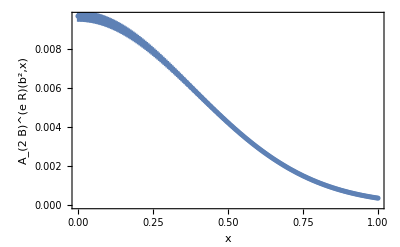

```mathematica
FourierA2bReelExpeta[9,-1,3, 3,12]
```

3 are SELECTED for fit!

3 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.4442(59)⟩_(RowBox[{)+bT^2 ⟨-0.04707(89)⟩_(RowBox[{)+bL^2 η ⟨-0.01205(29)⟩_(RowBox[{)) ⟨0.825(21)⟩_(RowBox[{), chisquareDoF = 7.05395
  = 9  = -2

12 is SELECTED for plot!

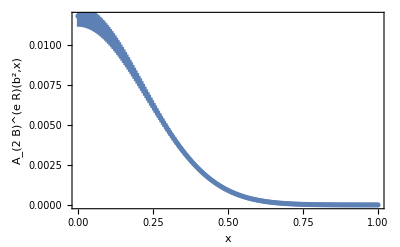

```mathematica
FourierA2bReelExpeta[9,-2,3, 3,12]
```

3 are SELECTED for fit!

3 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.468(15)⟩_(RowBox[{)+bT^2 ⟨-0.0553(27)⟩_(RowBox[{)+bL^2 η ⟨-0.01628(86)⟩_(RowBox[{)) ⟨0.846(56)⟩_(RowBox[{), chisquareDoF = 2.31714
  = 9  = -3

12 is SELECTED for plot!

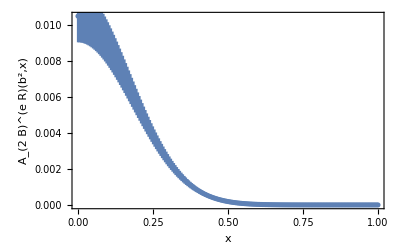

```mathematica
FourierA2bReelExpeta[9,-3,3, 3,12]
```

3 are SELECTED for fit!

3 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.445(37)⟩_(RowBox[{)+bT^2 ⟨-0.0653(75)⟩_(RowBox[{)+bL^2 η ⟨-0.0222(27)⟩_(RowBox[{)) ⟨0.81(14)⟩_(RowBox[{), chisquareDoF = 0.954065
  = 9  = -4

12 is SELECTED for plot!

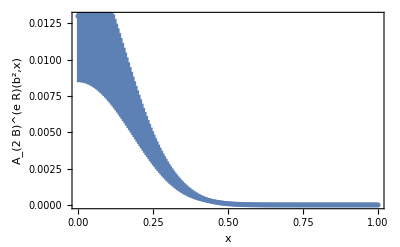

```mathematica
FourierA2bReelExpeta[9,-4,3, 3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.477(17)⟩_(RowBox[{)+bT^2 ⟨-0.0746(43)⟩_(RowBox[{)+bL^2 η ⟨-0.01142(67)⟩_(RowBox[{)) ⟨1.32(16)⟩_(RowBox[{), chisquareDoF = 1.54749
  = 9  = -2

12 is SELECTED for plot!

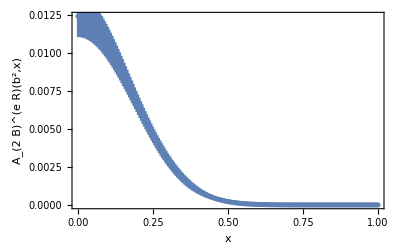

```mathematica
FourierA2bReelExpeta[9,-2,6, 3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.473(43)⟩_(RowBox[{)+bT^2 ⟨-0.088(12)⟩_(RowBox[{)+bL^2 η ⟨-0.0151(16)⟩_(RowBox[{)) ⟨1.15(38)⟩_(RowBox[{), chisquareDoF = 0.841819
  = 9  = -3

12 is SELECTED for plot!

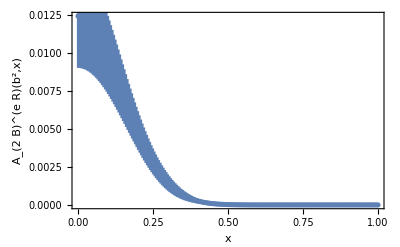

```mathematica
FourierA2bReelExpeta[9,-3,6, 3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.496(93)⟩_(RowBox[{)+bT^2 ⟨-0.069(19)⟩_(RowBox[{)+bL^2 η ⟨-0.0162(29)⟩_(RowBox[{)) ⟨0.89(70)⟩_(RowBox[{), chisquareDoF = 0.504828
  = 9  = -4

12 is SELECTED for plot!

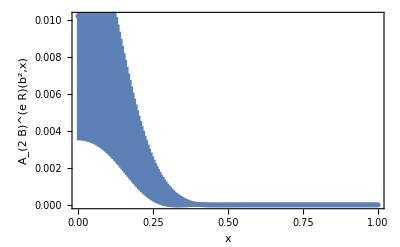

```mathematica
FourierA2bReelExpeta[9,-4,6, 3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.4560(83)⟩_(RowBox[{)+bT^2 ⟨-0.0577(16)⟩_(RowBox[{)+bL^2 η ⟨-0.00865(29)⟩_(RowBox[{)) ⟨1.179(66)⟩_(RowBox[{), chisquareDoF = 4.77692
  = 9  = -1

12 is SELECTED for plot!

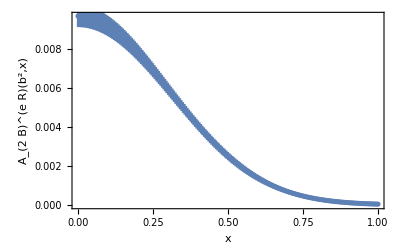

```mathematica
FourierA2bReelExpeta[9,-1,6, 3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.4560(83)⟩_(RowBox[{)+bT^2 ⟨-0.0577(16)⟩_(RowBox[{)+bL^2 η ⟨-0.00865(29)⟩_(RowBox[{)) ⟨1.179(66)⟩_(RowBox[{), chisquareDoF = 4.77692
  = 9  = -1

18 is SELECTED for plot!

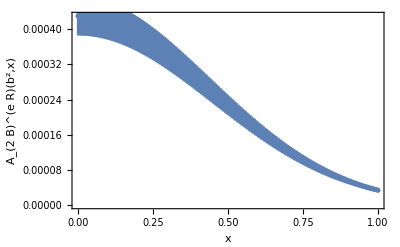

```mathematica
FourierA2bReelExpeta[9,-1,6, 3,18]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.4560(83)⟩_(RowBox[{)+bT^2 ⟨-0.0577(16)⟩_(RowBox[{)+bL^2 η ⟨-0.00865(29)⟩_(RowBox[{)) ⟨1.179(66)⟩_(RowBox[{), chisquareDoF = 4.77692
  = 9  = -1

25 is SELECTED for plot!

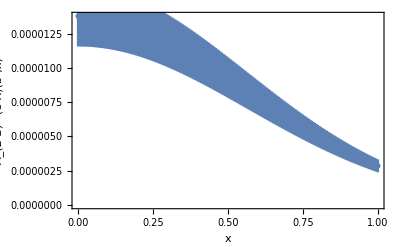

```mathematica
FourierA2bReelExpeta[9,-1,6, 3,25]
```

```mathematica
FourierA2bReelExpetaTog[b2_,P1_,etaminForFit_, bminForFit_, etafit_]:=Module[{dataforfitA12B, dataforfitA2B, dataforfitImA2B, fitJKA12B, fitParasA12B, chisqfitA12B, fitJKA2B, fitParasA2B, chisqfitA2B, fitJKImA2B, fitParasImA2B, chisqfitImA2B,fourierA2Bforx,fourierREA2Bforx},
dataforfitA2B = Select[MemDBGet[AmpDB,MemDBSelect[AmpDB,{A->A2B,PL->P1, bNum->even}],{etav, bL, bT,data}],#[[1]]>=etaminForFit&&Sqrt[#[[2]]^2+#[[3]]^2]>=bminForFit&];
Print["",bminForFit," are SELECTED for fit!"];
Print["",etaminForFit," are SELECTED for fit!"];
modelfitA2B[x1_,x2_, x3_,{a_,c_, d_,f_, g_}]:=a*Exp[-c*x1^g*x2^2]*Exp[-d*x3^2]*Exp[-f*x1];
fitJKA2B =JackknifeFit4D[dataforfitA2B,modelfitA2B[n, bL,bT,{a,c, d, f, g}],{{a, 1.32},{c,0.01142}, {d,0.0746}, {f,0.477}, {g,0.001}},{n,bL,bT}, modelfitA2B];
fitParasA2B=FitParameters/. fitJKA2B;
chisqfitA2B=chisquareDoF/. fitJKA2B; 
Print[modelfitA2B[,,,{a,c, d,f}]];
Print["Fitting:   ",modelfitA2B[,bL,bT,fitParasA2B], ", chisquareDoF = ", chisqfitA2B, "\n  = ",b2, "  = ",P1];
b2II = b2*fitParasA12B[[1]]/fitParasA12B[[1]];
II= fitParasA12B[[1]]/fitParasA12B[[1]];
fitaA2B =fitParasA2B[[1]];
fitcA2B=fitParasA2B[[2]];
fitdA2B =fitParasA2B[[3]];
fitfA2B =fitParasA2B[[4]];
fitgA2B =fitParasA2B[[5]];
A2BReprefactorPb=(((PowerJackk[etafit,fitgA2B])*fitcA2B)-fitdA2B)/(P1^2);
reducedratioA2B=fitaA2B/(Sqrt[2*A2BReprefactorPb]);
fourierA2B[x_, {reducedr_, A2BReprefactPb_, dA2B_, fA2B_}] :=Exp[-((x^2)/(4*A2BReprefactPb))-dA2B*b2]*Exp[-fA2B*etafit]*reducedr;

Print["",etafit," is SELECTED for plot!"];
fourieA2Bxforplot={};
Do[
fourierREA2Bforx=modelfitJackkifex[fourierA2B,{reducedratioA2B, A2BReprefactorPb, fitdA2B, fitfA2B}, x];
fourierA2Bforx=fourierREA2Bforx;
AppendTo[fourieA2Bxforplot,{x,fourierA2Bforx}];
,{x,0,1, 0.005}];
MkErrA2B=MakeErrBars[fourieA2Bxforplot];
PlotfourieA2Bx= ErrorListPlot[MkErrA2B,FrameLabel->{ , }, Frame->True , PlotRange->Full];
Print[PlotfourieA2Bx];
];
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.484(12)⟩_(RowBox[{)+bT^2 ⟨-0.0579(16)⟩_(RowBox[{)+bL^2 η^(⟨0.65(12)⟩_(RowBox[{)) ⟨-0.0165(35)⟩_(RowBox[{)) ⟨1.43(11)⟩_(RowBox[{), chisquareDoF = 4.58919
  = 9  = -1

12 is SELECTED for plot!

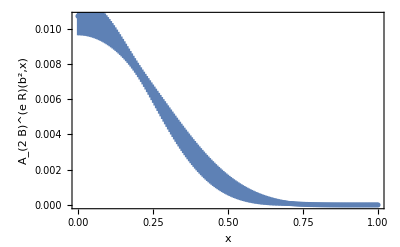

```mathematica
FourierA2bReelExpetaTog[9,-1,6, 3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.484(12)⟩_(RowBox[{)+bT^2 ⟨-0.0579(16)⟩_(RowBox[{)+bL^2 η^(⟨0.65(12)⟩_(RowBox[{)) ⟨-0.0165(35)⟩_(RowBox[{)) ⟨1.43(11)⟩_(RowBox[{), chisquareDoF = 4.58919
  = 9  = -1

18 is SELECTED for plot!

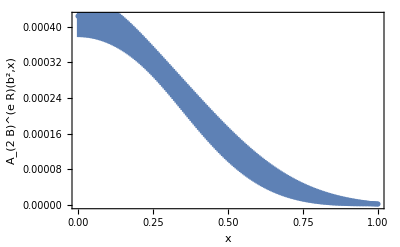

```mathematica
FourierA2bReelExpetaTog[9,-1,6, 3,18]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.484(12)⟩_(RowBox[{)+bT^2 ⟨-0.0579(16)⟩_(RowBox[{)+bL^2 η^(⟨0.65(12)⟩_(RowBox[{)) ⟨-0.0165(35)⟩_(RowBox[{)) ⟨1.43(11)⟩_(RowBox[{), chisquareDoF = 4.58919
  = 9  = -1

25 is SELECTED for plot!

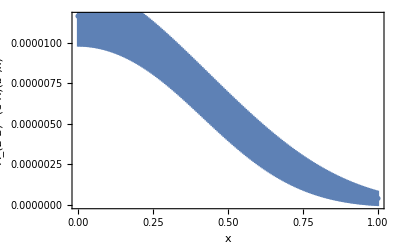

```mathematica
FourierA2bReelExpetaTog[9,-1,6, 3,25]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.512(23)⟩_(RowBox[{)+bT^2 ⟨-0.0753(45)⟩_(RowBox[{)+bL^2 η^(⟨0.62(21)⟩_(RowBox[{)) ⟨-0.0223(89)⟩_(RowBox[{)) ⟨1.68(27)⟩_(RowBox[{), chisquareDoF = 1.47249
  = 9  = -2

12 is SELECTED for plot!

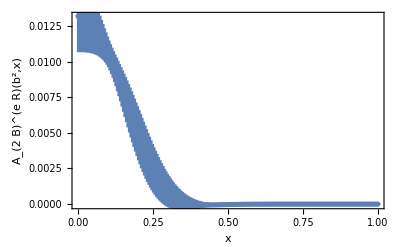

```mathematica
FourierA2bReelExpetaTog[9,-2,6, 3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.480(48)⟩_(RowBox[{)+bT^2 ⟨-0.088(12)⟩_(RowBox[{)+bL^2 η^(⟨0.92(42)⟩_(RowBox[{)) ⟨-0.013(14)⟩_(RowBox[{)) ⟨1.19(44)⟩_(RowBox[{), chisquareDoF = 0.834276
  = 9  = -3

12 is SELECTED for plot!

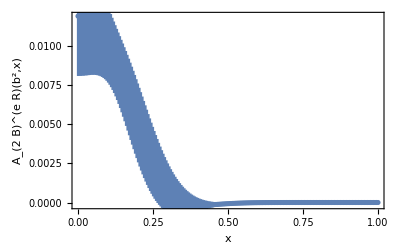

```mathematica
FourierA2bReelExpetaTog[9,-3,6, 3,12]
```

3 are SELECTED for fit!

6 are SELECTED for fit!

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.417(91)⟩_(RowBox[{)+bT^2 ⟨-0.068(18)⟩_(RowBox[{)+bL^2 η^(⟨1.91(66)⟩_(RowBox[{)) ⟨-0.0002 ± 0.0043⟩_(RowBox[{)) ⟨0.50(43)⟩_(RowBox[{), chisquareDoF = 0.484715
  = 9  = -4

12 is SELECTED for plot!

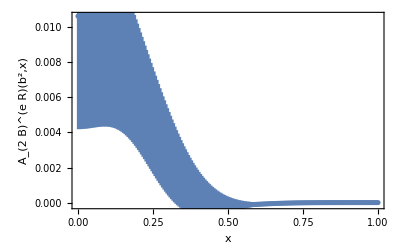

```mathematica
FourierA2bReelExpetaTog[9,-4,6, 3,12]
```

3 are SELECTED for fit!

3 are SELECTED for fit!

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.4807(43)⟩_(RowBox[{)+bT^2 ⟨-0.04062(44)⟩_(RowBox[{)+bL^2 η^(⟨0.334(33)⟩_(RowBox[{)) ⟨-0.02480(96)⟩_(RowBox[{)) ⟨1.043(17)⟩_(RowBox[{), chisquareDoF = 12.8342
  = 9  = -1

12 is SELECTED for plot!

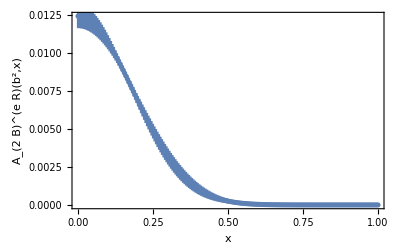

```mathematica
FourierA2bReelExpetaTog[9,-1,3, 3,12]
```

3 are SELECTED for fit!

3 are SELECTED for fit!

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.5180(87)⟩_(RowBox[{)+bT^2 ⟨-0.04734(91)⟩_(RowBox[{)+bL^2 η^(⟨0.326(61)⟩_(RowBox[{)) ⟨-0.0310(23)⟩_(RowBox[{)) ⟨1.132(37)⟩_(RowBox[{), chisquareDoF = 4.55152
  = 9  = -2

12 is SELECTED for plot!

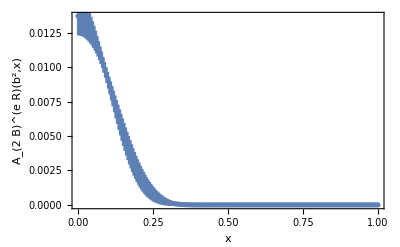

```mathematica
FourierA2bReelExpetaTog[9,-2,3, 3,12]
```

3 are SELECTED for fit!

3 are SELECTED for fit!

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.548(21)⟩_(RowBox[{)+bT^2 ⟨-0.0565(29)⟩_(RowBox[{)+bL^2 η^(⟨0.34(12)⟩_(RowBox[{)) ⟨-0.0411(57)⟩_(RowBox[{)) ⟨1.21(11)⟩_(RowBox[{), chisquareDoF = 1.763
  = 9  = -3

12 is SELECTED for plot!

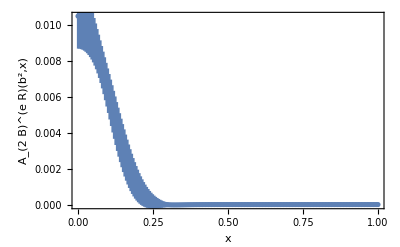

```mathematica
FourierA2bReelExpetaTog[9,-3,3, 3,12]
```

3 are SELECTED for fit!

3 are SELECTED for fit!

a ⅇ^(-f η-c η^2 b_L^2-d b_T^2)

Fitting:   ⅇ^(η ⟨-0.530(47)⟩_(RowBox[{)+bT^2 ⟨-0.0693(87)⟩_(RowBox[{)+bL^2 η^(⟨0.30(21)⟩_(RowBox[{)) ⟨-0.059(17)⟩_(RowBox[{)) ⟨1.25(26)⟩_(RowBox[{), chisquareDoF = 0.811584
  = 9  = -4

12 is SELECTED for plot!

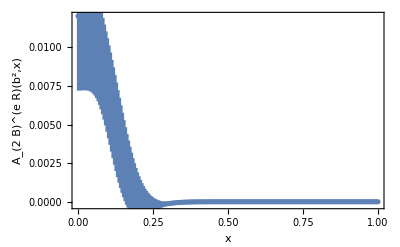

```mathematica
FourierA2bReelExpetaTog[9,-4,3, 3,12]
```